# A Month of Playing with Probability using Mathematica

## This notebook summarises all the copying I did from Nassim Taleb from his Tweets, his book, as well as his online MOOCs playlist. This summary was my attempt to get started in playing with probability using Mathematica/Wolfram Language.

## Learning probability through playing

This Mathematica notebook is an organised distillation of how I played with Mathematica to learn probability. This started with a fascination with the way Nassim Taleb did probability starting with Monte Carlo simulations. Unfortunately I do not have the luxury to learn it because of greed and fear of risks in the financial markets. Nor do I have the brains to think independently and come up with my own ideas. I only have the drive to get started with the remaining time I had with a Mathematica license from school. I did eventually end up purchasing Mathematica however.

This is in line with his recommendation to start with doing Monte Carlo simulations first, before trying to learn probability from a book.

## Connecting concepts with Mathematica

I wanted to start with some useful tips to use Mathematica as a computational explorer. For example, we can check the properties of any function in Mathematica with the following code.

```mathematica
?ReliabilityDistribution
```

This brings up the help for the particular function. The help function actually does a good job of explaining the function being used, with numerous examples within it.

To really explore the various concepts, we can actually find a relationship community graph of any Wolfram language function. This allows one to simply freely explore and take a look around of similar concepts.

```mathematica
Show[WolframLanguageData["ReliabilityDistribution", "RelationshipCommunityGraph"], ImageSize->600]
```

-Graphics-

Another technique I found useful in summarising an article is to import it using Mathematica and use one of the custom resource functions to delete the stopwords and plot a community graph plot of the relevant concepts.

```mathematica
CommunityGraphPlot[ResourceFunction["KeywordsGraph"][DeleteStopwords[Import["https://en.wikipedia.org/wiki/Monte_Carlo_method"]],50,VertexSize->"VertexWeight",EdgeStyle->Directive[Black,Dashed,Opacity[0.10]]],CommunityBoundaryStyle->Directive[Red,Dashed,Opacity[0.8]],ImageSize->600,GraphLayout->"RadialEmbedding"]
```

-Graphics-

## A comment on disinformation, ensembles versus anecdotes

To try and extrapolate the detail from the ensemble is to commit an error in the reverse of the law of large numbers. Therefore, it is important to be rigid and discuss the particular scale of the problem [3].

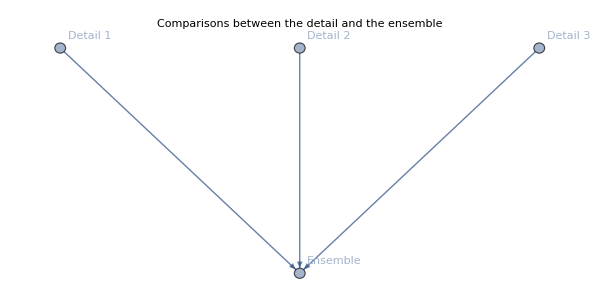

```mathematica
DirectedGraph[{"Detail 1"->"Ensemble","Detail 2"->"Ensemble","Detail 3"->"Ensemble"},VertexLabels->"Name",ImageSize->600, PlotLabel->"Comparisons between the detail and the ensemble"]
```

## A simple demo with the Central Limit Theorem

The Monte Carlo class of methods rely on repeatedly sampling from a selected distributions so that one can get numerical results. It is important to get an intuition for the problem using a Monte Carlo simulation to understand the truth. This avoids the green lumber problem.

One can consult the “Statistical Consequences of Fat Tails” [1] for a complete definition of the Central Limit Theorem, with the full textbook form. The main demonstration of how the central limit theorem fails for fat tailed distribution. This code takes the sum of 100 Pareto random variables, and runs this summation 10^5 times to form a histogram [2].

Before we begin, here is a reminder of the PostFix form.

```mathematica
?//
```

This will be used to create a table that sums a random variable drawn from a probability distribution.

```mathematica
?ParetoDistribution
```

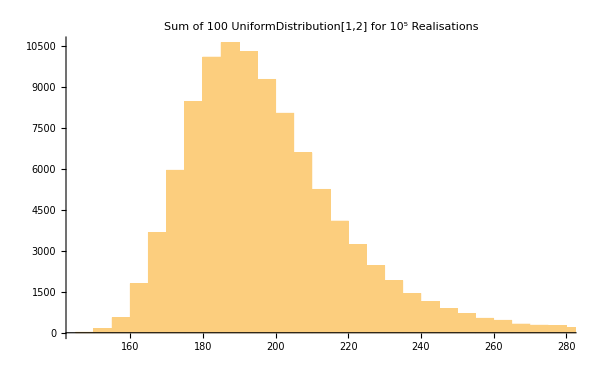

```mathematica
distpareto := RandomVariate[ParetoDistribution[1,2]];
Histogram[Table[Table[distpareto,{100}]//Total,{10^5}], PlotLabel->"Sum of 100 UniformDistribution[1,2] for 10^5 Realisations", ImageSize->600]
```

The central limit theorem fail here simply because the number of realisations for the variable is not infinity. This is pre-asymptotics. Note that the sum of the uniform distribution quickly looks like the Gaussian in contrast. This motivates the study of fat tailed distributions like the Pareto distribution. Repeat the same logic for the uniform distribution.

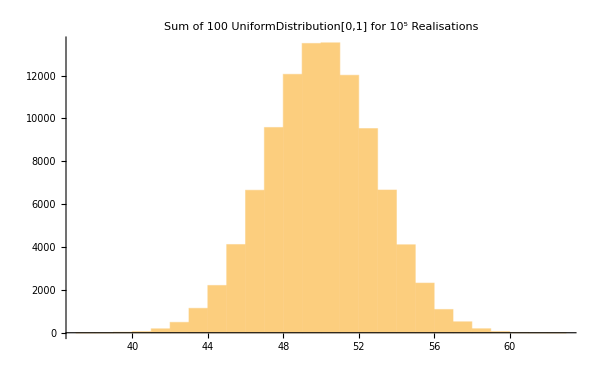

```mathematica
distuniform:= RandomVariate[UniformDistribution[]];
Histogram[Table[Table[distuniform,{100}]//Total,{10^5}], PlotLabel->"Sum of 100 UniformDistribution[0,1] for 10^5 Realisations", ImageSize->600]
```

Here is the how the uniform distributions looks closer and closer to the normal distribution.

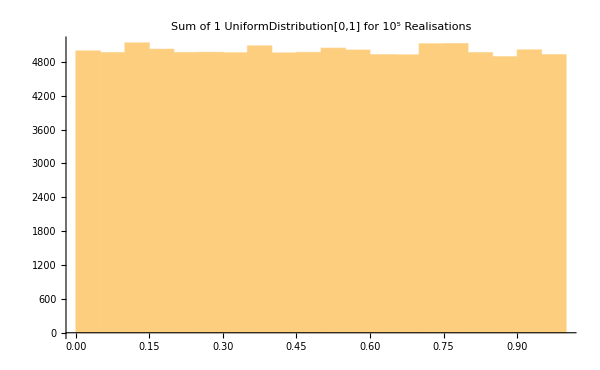

```mathematica
Histogram[Table[distuniform,{10^5}], PlotLabel->"Sum of 1 UniformDistribution[0,1] for 10^5 Realisations", ImageSize->600]
```

It looks like a triangle when we take the sum twice.

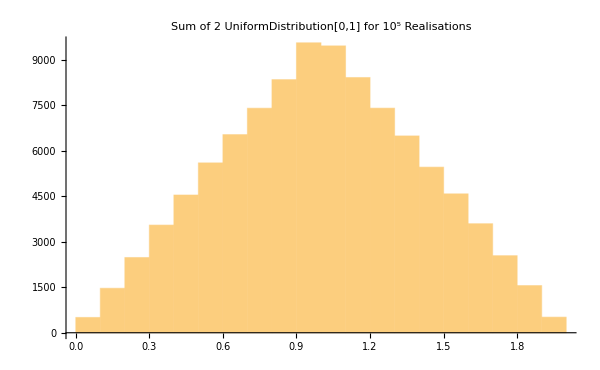

```mathematica
Histogram[Table[Sum[distuniform,{i,1,2}],{10^5}], PlotLabel->"Sum of 2 UniformDistribution[0,1] for 10^5 Realisations", ImageSize->600]
```

Now we take this sum 10 times, and it already looks fairly close to a normal distribution.

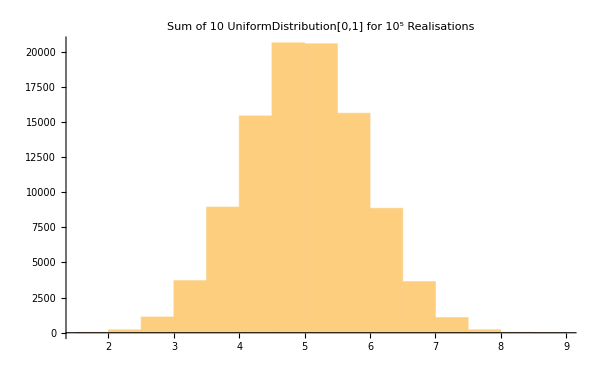

```mathematica
Histogram[Table[Sum[distuniform,{i,1,10}],{10^5}], PlotLabel->"Sum of 10 UniformDistribution[0,1] for 10^5 Realisations", ImageSize->600]
```

### Application of the Uniform Distribution: Miles Per Annum cannot be uniform

Dan Ariely conducted a study on the distribution of miles driven. The standard deviation was unusually high, with it being half the mean. This must be (roughly) a uniform distribution, however miles per annum cannot be uniform since they are cumulative.

One can reverse engineer to get the left and right bounds of the uniform distribution obtained using Mathematica. Before this, here are some quick reminders on the properties of the uniform distribution.

```mathematica
?UniformDistribution
```

```mathematica
Show[WolframLanguageData["UniformDistribution", "RelationshipCommunityGraph"], ImageSize->600]
```

-Graphics-

```mathematica
Mean[UniformDistribution[{a,b}]]
```

(a+b)/2

```mathematica
StandardDeviation[UniformDistribution[{a,b}]]
```

(-a+b)/(2 √3)

Now we can attempt to reverse engineer the fabricated (approximately) uniform distribution given the mean and the standard deviation.

```mathematica
uniformsolve1=Solve[{(a+b)/2==23670,(b-a)/(2 √3)==12621},{a,b}]//Flatten//N
```

{a→1809.79,b→45530.2}

Of course, you can do this with other distributions.

```mathematica
uniformsolve2=Solve[{(a+b)/2==26094,(b-a)/(2 √3)==12253},{a,b}]//Flatten//N
```

{a→4871.18,b→47316.8}

```mathematica
?UniformDistribution
```

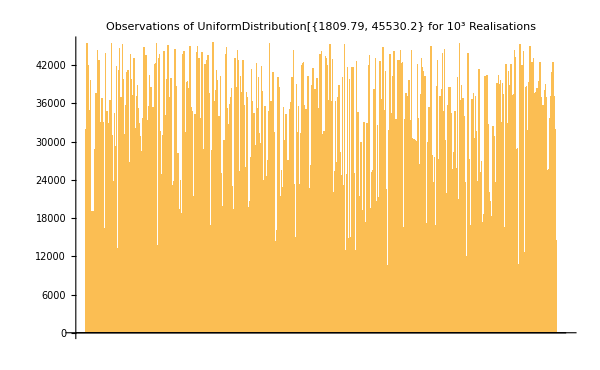

```mathematica
BarChart[Table[RandomVariate[UniformDistribution[{1809.79, 45530.2}]],{1000}], PlotLabel->"Observations of UniformDistribution[{1809.79, 45530.2} for 10^3 Realisations", ImageSize->600]
```

## The Pareto distribution, and the law of large numbers

The power law class is very interesting, somehow it does not get to a steady value with increasing number of realisations.

```mathematica
?ParetoDistribution
```

I found it easy to just use this to copy paste the definitions here so that it is easy to compare and refer to.

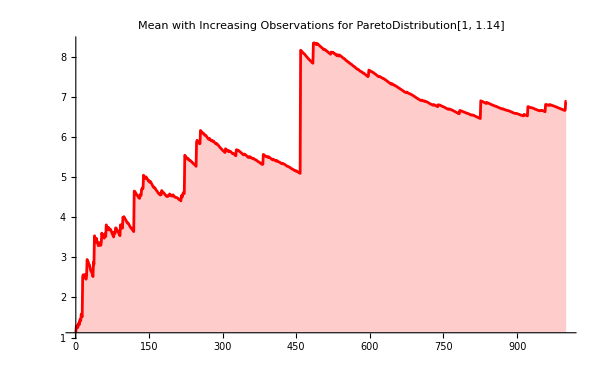

```mathematica
distpareto2 := RandomVariate[ParetoDistribution[1,1.14]];
tapareto2 = Table[distpareto2,{1000}];
DiscretePlot[Mean[tapareto2[[1;;i]]],{i,1,Length[tapareto2]},PlotStyle->Red, PlotRange->All, ImageSize->600, PlotLabel->"Mean with Increasing Observations for ParetoDistribution[1, 1.14]"]
```

Compare this to a normal distribution. This one settles at the mean very quickly.

```mathematica
?NormalDistribution
```

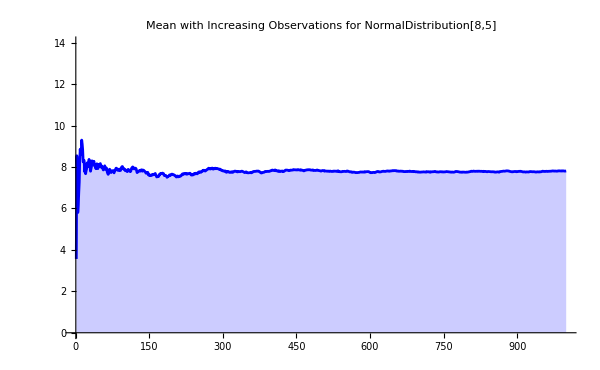

```mathematica
distnorm2 := RandomVariate[NormalDistribution[8,5]];
tanorm2 = Table[distnorm2,{1000}];
DiscretePlot[Mean[tanorm2[[1;;i]]],{i,1,Length[tanorm2]},PlotStyle->Blue, PlotRange->{0,14}, ImageSize->600,PlotLabel->"Mean with Increasing Observations for NormalDistribution[8,5]"]
```

We can compare the bar charts of these two tables.

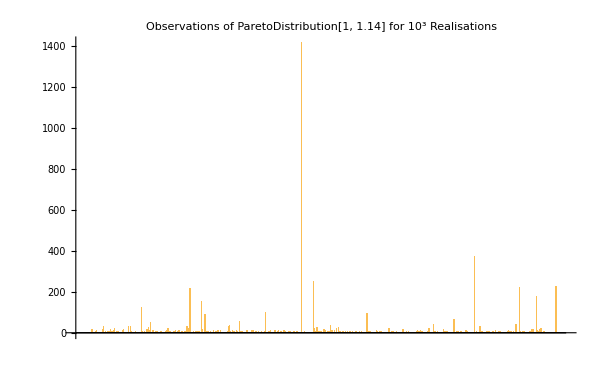

```mathematica
BarChart[tapareto2, PlotLabel->"Observations of ParetoDistribution[1, 1.14] for 10^3 Realisations", ImageSize->600]
```

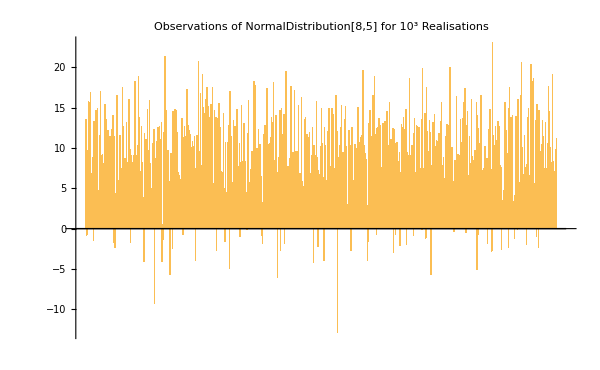

```mathematica
BarChart[tanorm2, PlotLabel->"Observations of NormalDistribution[8,5] for 10^3 Realisations", ImageSize->600]
```

We can see how the various distributions are related to the Pareto distribution based on this. In fact,t he next of our interest is the stable distribution which we will discuss later.

## Looking at the Pareto distribution a bit more carefully

With Mathematica, one can see how the distributions are related. You can consult Wikipedia for more information here: https://en.wikipedia.org/wiki/Pareto_distribution.

```mathematica
Show[WolframLanguageData["ParetoDistribution", "RelationshipCommunityGraph"], ImageSize->600]
```

-Graphics-

```mathematica
?ParetoDistribution
```

One can see how the parameters change with these parameters. We can set the sliders to change.

```mathematica
Manipulate[Module[{dist,plot},dist=ParetoDistribution[k,alpha];
plot=Plot[PDF[dist,x],{x,0,10},PlotRange->All,
PlotStyle->Blue,
ImageSize->600,
PlotLabel->Row[{"Pareto Distribution: α = ",alpha}]]],{{alpha,1,"Shape Parameter (α)"},0.1,2,0.1},{{k,0.1,"Minimum Value Parameter (k)"},0.1,10,0.1}]
```

### Visualising the effect of power laws

In the power law class, the rare event contributes to most of the properties. One can study this by looking at the inverse survival function of the Pareto distribution. Recall that the survival function is the probability of a variable exceeding a given parameter. There is actually a closed form one can pull out with Mathematica [5].

We solve for the survival function such that K exceeds L where L is the minimum value parameter of the Pareto distribution for a particular shape parameter α.

```mathematica
?ParetoDistribution
```

```mathematica
solK= Solve[FullSimplify[SurvivalFunction[ParetoDistribution[L,α],K],K>L] == p, K]//Quiet
```

{{K→L p^(-1/α)}}

We can use Mathematica to get a share of a particular quantile given the associated tail exponent.

```mathematica
?PowerExpand
```

We can find the probability of exceeding of a certain threshold to get this expression. We do this by finding the normalised expression using the integral of the value multiplied by its associated PDF for all cases past K towards infinity divided by the mean of the Pareto distribution. This allows us to get the proportion of the threshold of the body required.

```mathematica
threshold = Integrate[x PDF [ParetoDistribution[L,α],x],{x,K,∞},Assumptions->K>L>α>1]/Simplify[Mean[ParetoDistribution[L,α]],Assumptions->K>L>α>1]/.solK[[1]] // PowerExpand // FullSimplify
```

p^((-1+α)/α)

We can for example solve for the tail exponent of the 80/20 rule, where 20% of the people own 80% of the land, as classically defined by Pareto. This gives the tail exponent to be α = 1.16096.

```mathematica
Solve[(threshold/.p->0.2)==0.8,α]//Quiet
```

{{α→1.16096}}

We can check how much the top 1% own (1/100), we find that the top 1% must own about 52.8% of the land under the Pareto distribution.

```mathematica
threshold /.α->1.16096 /.p -> (1/100)//N
```

0.528095

```mathematica
TableForm[Table[{a,1-a,Solve[(threshold/.p->a)==1-a,α]},{a,0,0.4,0.01}],TableHeadings->{None,{"Minority Ratio (p)","Majority ratio (1-p)" ,"Tail exponent (α)"}}] //Quiet
```

Minority Ratio (p) | Majority ratio (1-p) | Tail exponent (α)
0. | 1. | 
0.01 | 0.99 | α→1.00219
0.02 | 0.98 | α→1.00519
0.03 | 0.97 | α→1.00876
0.04 | 0.96 | α→1.01284
0.05 | 0.95 | α→1.01742
0.06 | 0.94 | α→1.02249
0.07 | 0.93 | α→1.02806
0.08 | 0.92 | α→1.03414
0.09 | 0.91 | α→1.04076
0.1 | 0.9 | α→1.04795
0.11 | 0.89 | α→1.05574
0.12 | 0.88 | α→1.06416
0.13 | 0.87 | α→1.07326
0.14 | 0.86 | α→1.08308
0.15 | 0.85 | α→1.09369
0.16 | 0.84 | α→1.10514
0.17 | 0.83 | α→1.11751
0.18 | 0.82 | α→1.13087
0.19 | 0.81 | α→1.14532
0.2 | 0.8 | α→1.16096
0.21 | 0.79 | α→1.17791
0.22 | 0.78 | α→1.19631
0.23 | 0.77 | α→1.21631
0.24 | 0.76 | α→1.23809
0.25 | 0.75 | α→1.26186
0.26 | 0.74 | α→1.28787
0.27 | 0.73 | α→1.31641
0.28 | 0.72 | α→1.34782
0.29 | 0.71 | α→1.38251
0.3 | 0.7 | α→1.42096
0.31 | 0.69 | α→1.46376
0.32 | 0.68 | α→1.51164
0.33 | 0.67 | α→1.5655
0.34 | 0.66 | α→1.62644
0.35 | 0.65 | α→1.69589
0.36 | 0.64 | α→1.77566
0.37 | 0.63 | α→1.86813
0.38 | 0.62 | α→1.97648
0.39 | 0.61 | α→2.10504
0.4 | 0.6 | α→2.25985

Of course we could be a lot more strict. However with this logic of minority ratio and majority ratio being such that the sum is 1, the tail exponent does not seem to go below 1. This shows that errors in the tail exponent can lead to very serious mistakes.

```mathematica
TableForm[Table[{a,1-a,Solve[(threshold/.p->a)==1-a,α]},{a,0,0.01,0.001}],TableHeadings->{None,{"Minority Ratio (p)","Majority ratio (1-p)" ,"Tail exponent (α)"}}]//Quiet
```

Minority Ratio (p) | Majority ratio (1-p) | Tail exponent (α)
0. | 1. | 
0.001 | 0.999 | α→1.00014
0.002 | 0.998 | α→1.00032
0.003 | 0.997 | α→1.00052
0.004 | 0.996 | α→1.00073
0.005 | 0.995 | α→1.00095
0.006 | 0.994 | α→1.00118
0.007 | 0.993 | α→1.00142
0.008 | 0.992 | α→1.00167
0.009 | 0.991 | α→1.00192
0.01 | 0.99 | α→1.00219

## References

Please forgive me if I did not reference a particular Tweet from Nassim Taleb.

[1] Nassim Nicholas Taleb. Statistical Consequences of Fat Tails: Revised Edition (2022). Accessed: Jan. 2, 2024. Available: https://arxiv.org/pdf/2001.10488.pdf
[2] Nassim Nicholas Taleb. Doing Probability with Mathematica (2019). Accessed: Jan. 2, 2024. Available: https://www.youtube.com/watch?v=JTz4wkD-mxU
[3] Nassim Nicholas Taleb. Disinformation and Fooled By Randomness (2023). Accessed. Jan. 2. 2024. Available: https://www.youtube.com/watch?app=desktop&v=T3ScFshhhnU 
[4] Nassim Nicholas Taleb. Comments on Ariely Honesty Paper (2021). Accessed. Jan. 3. 2024. 
Available: https://twitter.com/nntaleb/status/1429295773938814978?lang=en 
[5] Nassim Nicholas Taleb. MINI LECTURE 8c: A simple tricks to see the effect of power laws (2021). Accessed. Jan. 3. 2024. Available: https://www.youtube.com/watch?v=XhTHG3QmVwM